# NDSolve/WhenEvent vs ItoProcess: a continuously measured qubit's trajectory

A companion to Trajectories, the Record, and the Master Equation. There the free particle is watched on a grid; here the object is a continuously monitored qubit, whose complete state is the three Bloch numbers ⟨(σ̂)_x⟩,⟨(σ̂)_y⟩,⟨(σ̂)_z⟩ living in the ball r=|{x,y,z}|≤1. The trajectory is a Cartesian-Bloch Ito SDE, integrated natively by the built-in RandomFunction[ItoProcess[...]]. NDSolve has no native Wiener input, so this document hand-rolls Euler-Maruyama inside NDSolve via WhenEvent, and asks a sharp question: does the hand-rolled route reproduce the built-in ensemble and the Lindblad master equation, while keeping r≤1, and at what cost? Every number below is produced by a cell you can rerun.

Mads Bahrami (last updated: July 29, 2026)

This document is nearly self-contained: evaluate the cells top to bottom, and the only external ingredient is one Wolfram Function Repository function, ItoProcessChangeVariables, which performs the Ito change of variables for the r≤1 proof and is fetched automatically on first use. The six rates {Γ_CI,Γ_BA,Γ_d,γ_ϕ,γ_1,Ω_x} (measurement coherent-information, backaction dephasing, measurement dephasing Γ_m/2, pure dephasing, 1/T_1, and Rabi) stay symbolic where the algebra is symbolic and become numbers only when we simulate. The code uses these same Greek letters for the rates, so it reads like the formulas.

## From the density matrix to the Bloch SDE

The trajectory follows from continuous homodyne detection of (σ̂)_z (Gambetta07), with T_1 decay, pure dephasing, and a Rabi drive. Homodyne detection beats the cavity's output field against a strong local-oscillator reference at the same frequency, so the recorded photocurrent reads out one chosen field quadrature, here the one carrying the qubit's (σ̂)_z (which-state) information. Write the effective transverse rate as Γ_2^eff=γ_1/2+γ_ϕ+Γ_d=1/T_2^eff. The object actually being tracked is the conditional density matrix ρ, which obeys a stochastic master equation, a deterministic Lindblad drift plus a state-dependent measurement backaction along the record's noise:

dρ=((-i[H,ρ]+γ_1 𝒟[(σ̂)_-]ρ+(γ_ϕ+Γ_d)/2 𝒟[(σ̂)_z]ρ)_(Lindblad drift)) dt + (ℋ[c]ρ)_(homodyne backaction) dW,

with the Rabi Hamiltonian H=Ω_x/2(σ̂)_x, the GKSL dissipator 𝒟[L]ρ=Lρ L^†-1/2{L^†L,ρ}, and the homodyne measurement (innovation) superoperator ℋ[c]ρ=cρ+ρ c^†-Tr[(c+c^†)ρ] ρ (Wiseman-Milburn; the calligraphic ℋ is the measurement superoperator, not the Hamiltonian H), with measurement operator c=1/2(√Γ_CI-i √Γ_BA)(σ̂)_z. Here Γ_CI weights the informative quadrature that sharpens the state toward a (σ̂)_z eigenstate, and Γ_BA the orthogonal quadrature that only kicks the phase.

Projected onto the Bloch vector {x,y,z}={⟨(σ̂)_x⟩,⟨(σ̂)_y⟩,⟨(σ̂)_z⟩}, the Lindblad drift becomes the dt terms and the backaction the dW terms of a single scalar-noise Ito SDE:

d(x
y
z)=(-Γ_2^eff x
-Γ_2^eff y-Ω_x z
γ_1(1-z)+Ω_x y)_(a⃗) dt + (-√Γ_CI xz-√Γ_BA y
-√Γ_CI yz+√Γ_BA x
√Γ_CI (1-z^2))_(b⃗) dW.

This is the standard split d v⃗=a⃗(v⃗) dt+b⃗(v⃗) dW with v⃗={x,y,z}: the two labeled columns are the drift vector a⃗ (the dt part) and the diffusion vector b⃗ (the dW part, a single column since one scalar noise dW drives all three components). In code, the drift, with the transverse rate Γ_2^eff folded in:

```mathematica
driftV[{x_, y_, z_}, {ΓCI_, ΓBA_, Γd_, γϕ_, γ1_, Ωx_}] :=
  With[{Γ2eff = γ1/2 + γϕ + Γd},
   {-Γ2eff x, -Γ2eff y - Ωx z, γ1 (1 - z) + Ωx y}];
```

And the diffusion b⃗, the second column above:

```mathematica
diffV[{x_, y_, z_}, {ΓCI_, ΓBA_, Γd_, γϕ_, γ1_, Ωx_}] :=
  {-Sqrt[ΓCI] x z - Sqrt[ΓBA] y,
   -Sqrt[ΓCI] y z + Sqrt[ΓBA] x,
   Sqrt[ΓCI] (1 - z^2)};
```

The native route hands {a⃗,b⃗} to ItoProcess and integrates with RandomFunction using the SDE-native scalar-noise stochastic Runge-Kutta. The hand-rolled route freezes the ODE (x'[t]==0) inside NDSolve and injects one explicit Euler-Maruyama step at each dt through a WhenEvent, adding a⃗ dt+b⃗ dW to the current state. Two mistakes to avoid: do not integrate the drift in the ODE and re-add it in the event (double count), and the event must ADD the increment to the state, not replace the state with it.

## The mean is the Lindblad equation, exactly

The drift is affine in {x,y,z}: a⃗(v⃗)=A v⃗+c⃗. Taking the Ito expectation kills the dW term (𝔼[b⃗ dW]=0), so the mean ⟨v⃗⟩=𝔼[v⃗] obeys a closed, deterministic linear ODE,

(d⟨x⟩)/dt=-Γ_2^eff⟨x⟩,  (d⟨y⟩)/dt=-Γ_2^eff⟨y⟩-Ω_x⟨z⟩,  (d⟨z⟩)/dt=γ_1(1-⟨z⟩)+Ω_x⟨y⟩,

which is exactly the Bloch form of the Lindblad drift above: transverse decay at Γ_2^eff, relaxation to the ground state at γ_1, and the Rabi rotation Ω_x. Solve it symbolically with DSolve:

```mathematica
Clear[Γ2eff, γ1, Ωx, x0, y0, z0];
meanSol = DSolve[{X'[t] == -Γ2eff X[t], Y'[t] == -Γ2eff Y[t] - Ωx Z[t],
    Z'[t] == γ1 (1 - Z[t]) + Ωx Y[t], X[0] == x0, Y[0] == y0, Z[0] == z0},
   {X, Y, Z}, t] // First;
```

The transverse component decouples and decays as a pure exponential, ⟨x⟩(t)=x_0 e^(-Γ_2^eff t), while ⟨y⟩,⟨z⟩ form a damped Rabi pair:

```mathematica
X[t] /. meanSol
```

ⅇ^(-t Γ2eff) x0

So the ensemble mean of the trajectory SDE is the Lindblad master equation, identically. The mean sees only the drift; it is blind to any diffusion that leaves the drift alone, which makes matching it a weak test. We sharpen it with the second moment below.

## The ball r≤1 is an invariant, proven

Positivity of the qubit density matrix is exactly r≤1, because ρ=(I+x(σ̂)_x+y(σ̂)_y+z(σ̂)_z)/2 has det ρ=(1-r^2)/4, which is non-negative iff r≤1. The cleanest way to see that the SDE respects this is to change coordinates from Cartesian {x,y,z} to spherical {r,θ,ϕ} and read off the radius's own one-dimensional Ito equation dr=a_r dt+b_r dW: its two coefficients settle the invariant directly. Build the Cartesian process symbolically first:

```mathematica
Clear[x, y, z, x0, y0, z0, ΓCI, ΓBA, Γd, γϕ, γ1, Ωx];
ratesSym = {ΓCI, ΓBA, Γd, γϕ, γ1, Ωx};
procSym = ItoProcess[{driftV[{x, y, z}, ratesSym], List /@ diffV[{x, y, z}, ratesSym], {x, y, z}},
   {{x, y, z}, {x0, y0, z0}}, t];
```

The Wolfram Function Repository's ItoProcessChangeVariables applies Ito's rule, including the second-order correction, to rewrite the SDE in spherical coordinates. This is the one external ingredient in the document, fetched automatically on first use:

```mathematica
sphProc = ResourceFunction["ItoProcessChangeVariables"][procSym, {r, θ, ϕ}, "Cartesian" -> "Spherical"];
```

First the noise. The radial diffusion coefficient b_r is the top entry of the transformed diffusion:

```mathematica
FullSimplify[sphProc["Diffusion"][[1, 1]], Assumptions -> {r[t] > 0}]
```

-√ΓCI Cos[θ[t]] (-1+r[t]^2)

It is proportional to (1-r^2), namely b_r=√Γ_CI cos θ (1-r^2), so it vanishes on the surface r=1 for every choice of rates. The measurement noise is tangent to the Bloch sphere: a noise step slides the state along the sphere and never off it.

Second the drift. Evaluate the radial drift a_r on the surface r=1:

```mathematica
Clear[η];
radialDrift = FullSimplify[sphProc["Drift"][[1]] /. r[t] -> 1, Assumptions -> {0 <= θ[t] <= Pi}];
```

Write the measurement efficiency as η=(Γ_CI+Γ_BA)/(2 Γ_d) and ask Reduce whether any point on the sphere, for any physical efficiency η∈ and non-negative rates, can make the radial drift point outward, a_r>0:

```mathematica
Reduce[(radialDrift /. ΓBA -> 2 η Γd - ΓCI) > 0 &&
   0 <= θ[t] <= Pi && γ1 >= 0 && γϕ >= 0 && Γd >= 0 &&
   ΓCI >= 0 && 2 η Γd - ΓCI >= 0 && 0 <= η <= 1, {θ[t]}]
```

False

False: no such point exists, so a_r≤0 everywhere on r=1. The noise cannot push the state off the sphere and the drift can only pull it inward, so the exact continuous flow never leaves the ball. Discrete integrators are another matter, which is the whole point of what follows.

## The three integrators

The native route builds an ItoProcess from the drift, the diffusion (as a one-column matrix, since the noise is scalar), and the state variables, then lets RandomFunction integrate ntraj paths on the grid {0,t_f,dt} with the SDE-native scalar-noise stochastic Runge-Kutta. The process variables are Wolfram's formal symbols, unbound by construction, so they are safe placeholders:

```mathematica
itoEnsemble[rates_, {x0_, y0_, z0_}, tf_, dt_, ntraj_, seed_] :=
  Module[{proc, td, vals},
   proc = ItoProcess[{driftV[{x[t], y[t], z[t]}, rates],
      List /@ diffV[{x[t], y[t], z[t]}, rates],
      {x[t], y[t], z[t]}},
     {{x, y, z}, {x0, y0, z0}}, t];
   td = BlockRandom[SeedRandom[seed];
     RandomFunction[proc, {0., tf, dt}, ntraj, Method -> "StochasticRungeKuttaScalarNoise"]];
   vals = td["ValueList"];   (* full data: ntraj x npts x 3, the {x,y,z} of every path *)
   <|"trajectories" -> vals, "times" -> td["Times"],
     "meanZ" -> Mean[vals[[All, All, 3]]], "zTrajs" -> vals[[All, All, 3]],
     "maxr" -> Max[Map[Norm, vals, {2}]]|>];
```

Both ensemble builders keep the full simulated data: the returned association carries a trajectories key, an ntraj×npts×3 array of the Bloch vector {x,y,z} at every path and step, and meanZ, zTrajs, and maxr are convenience reductions of it.

The hand-rolled route is explicit Euler-Maruyama. For the SDE d v⃗=a⃗ dt+b⃗ dW the update is

(v⃗)_(n+1)=(v⃗)_n+a⃗((v⃗)_n) Δt+b⃗((v⃗)_n) Δ W_n,    Δ W_n∼𝒩(0,√Δt),

with an optional projection v⃗↦v⃗/max (1,Abs[v⃗]) that snaps any overshoot back onto the ball. One NDSolve carries three length-ntraj vectors; a single WhenEvent at each grid point draws ntraj Wiener increments ΔW (one per trajectory), reuses driftV/diffV, and applies the update. The midpoint event phase Mod[t+dt/2,dt]==0 fires exactly N=t_f/Δt times and samples cleanly on the grid:

```mathematica
emEnsemble[rates_, {x0_, y0_, z0_}, tf_, dt_, ntraj_, seed_, project_] :=
  Module[{xs, ys, zs, sol, grid, xyzg},
   sol = BlockRandom[SeedRandom[seed];
     NDSolve[{xs'[t] == ConstantArray[0., ntraj], ys'[t] == ConstantArray[0., ntraj],
       zs'[t] == ConstantArray[0., ntraj],
       WhenEvent[Mod[t + dt/2, dt] == 0,
        Block[{ΔW = RandomVariate[NormalDistribution[0, Sqrt[dt]], ntraj], xyz, new, capr},
         xyz = {xs[t], ys[t], zs[t]};
         new = xyz + MapThread[#1 dt + #2 ΔW &, {driftV[xyz, rates], diffV[xyz, rates]}];
         capr = If[project, Clip[Sqrt[new[[1]]^2 + new[[2]]^2 + new[[3]]^2], {1., Infinity}],
                   ConstantArray[1., ntraj]];
         {xs[t], ys[t], zs[t]} -> (#/capr & /@ new)]],
       xs[0] == ConstantArray[N@x0, ntraj], ys[0] == ConstantArray[N@y0, ntraj],
       zs[0] == ConstantArray[N@z0, ntraj]},
      {xs, ys, zs}, {t, 0, tf}, MaxStepSize -> dt][[1]]];
   grid = Range[0., tf, dt];
   xyzg = ({xs[#], ys[#], zs[#]} /. sol) & /@ grid;   (* npts x 3 x ntraj *)
   <|"trajectories" -> Transpose[xyzg, {2, 3, 1}],   (* full data: ntraj x npts x 3 *)
     "times" -> grid, "meanZ" -> Mean /@ xyzg[[All, 3]],
     "zTrajs" -> Transpose[xyzg[[All, 3]]],
     "maxr" -> Max[Sqrt[xyzg[[All, 1]]^2 + xyzg[[All, 2]]^2 + xyzg[[All, 3]]^2]]|>];
```

The exact reference is the mean ODE from the first section, which closes in a DSolve closed form (no integration error). Wrapped as a function of the rates, initial state, and time, it returns the full mean Bloch vector ⟨v⃗⟩(t)={⟨x⟩,⟨y⟩,⟨z⟩}(t); its third component is ⟨z⟩:

```mathematica
lindbladBloch[rates_, {x0_, y0_, z0_}] :=
  Module[{ΓCI, ΓBA, Γd, γϕ, γ1, Ωx, Γ2eff, sol},
   {ΓCI, ΓBA, Γd, γϕ, γ1, Ωx} = rates;
   Γ2eff = γ1/2 + γϕ + Γd;
   sol = DSolve[{x'[t] == -Γ2eff x[t],
      y'[t] == -Γ2eff y[t] - Ωx z[t],
      z'[t] == γ1 (1 - z[t]) + Ωx y[t],
      x[0] == x0, y[0] == y0, z[0] == z0},
     {x, y, z}, t] // First;
   Function[tt, Re[{x[tt], y[tt], z[tt]} /. sol]]];   (* {<x>,<y>,<z>}(tt) *)
```

## Reproduction on a clean dimensionless case

Rescaling every rate by γ_1 makes the physics dimensionless without changing it: the trajectory in τ=γ_1 t is identical, and the dimensionless ratios that survive are what matter. Take the decoherence structure of a representative dispersive transmon (30/20 μs for T_1/T_2, a weak readout), rescaled by γ_1, which gives {Γ_CI,Γ_BA,Γ_d,γ_ϕ,γ_1}/γ_1={0.352,0,0.176,1,1} with efficiency η=(Γ_CI+Γ_BA)/(2 Γ_d)=1 (optimal homodyne phase). Pair it with a deliberately gentle drive Ω_x/γ_1=3, from a ground-state start {0,0,1}. The drive is gentled on purpose so the explicit scheme sits well inside its stability window; the true transmon drive is about sixty times faster, and that stiff case is the honest catch below. The rate vector is positional, {Γ_CI,Γ_BA,Γ_d,γ_ϕ,γ_1,Ω_x}:

```mathematica
ratesB = {0.352, 0., 0.176, 1., 1., 3.}; initB = {0., 0., 1.}; tfB = 3.; nB = 1000;
```

First the exact reference: the affine mean ODE closed in DSolve form, evaluated as a function of time (its third component is ⟨z⟩):

```mathematica
lindB = lindbladBloch[ratesB, initB];
```

Next the native route, integrating n trajectories of the ItoProcess with the SDE-native scalar-noise stochastic Runge-Kutta:

```mathematica
itoB = itoEnsemble[ratesB, initB, tfB, tfB/600, nB, 2024];
```

Then the hand-rolled route, the same ensemble through the projected Euler-Maruyama inside NDSolve/WhenEvent:

```mathematica
emB = emEnsemble[ratesB, initB, tfB, tfB/600, nB, 2024, True];
```

Compare the exact final ⟨z⟩ against the two ensemble means:

```mathematica
{lindB[tfB][[3]], Last[itoB["meanZ"]], Last[emB["meanZ"]]}
```

{0.146666,0.152979,0.146814}

Both ensemble means land within the Monte-Carlo scatter 1/√n of the exact Lindblad, which is the sense in which they agree. As curves, the two ensemble means track the exact black line:

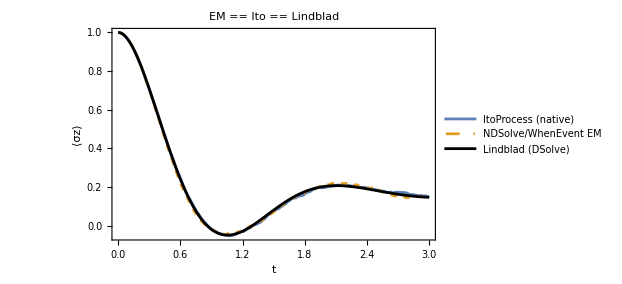

```mathematica
ListLinePlot[{Transpose[{itoB["times"], itoB["meanZ"]}],
   Transpose[{emB["times"], emB["meanZ"]}],
   Transpose[{itoB["times"], lindB[#][[3]] & /@ itoB["times"]}]},
  PlotStyle -> {ColorData[97, 1], Directive[Dashed, ColorData[97, 2]], Directive[Thick, Black]},
  PlotLegends -> {"ItoProcess (native)", "NDSolve/WhenEvent EM", "Lindblad (DSolve)"},
  Frame -> True, FrameLabel -> {"t", "⟨σz⟩"},
  ImageSize -> 460, PlotLabel -> "EM == Ito == Lindblad"]
```

Now the invariant. Run one more ensemble with the projection turned off, at a coarser step so any overshoot is visible:

```mathematica
emBnp = emEnsemble[ratesB, initB, tfB, tfB/50, nB, 2024, False];
```

Compare the largest Bloch radius reached along the way. The projected Euler-Maruyama holds the ball to machine precision, the native SRK overshoots it a little (it is not norm-preserving), and the unprojected Euler-Maruyama overshoots more, since off the sphere the noise is no longer tangent and nothing pulls the state back:

```mathematica
{"EM proj maxr" -> emB["maxr"], "Ito maxr" -> itoB["maxr"], "EM noProj maxr" -> emBnp["maxr"]}
```

{EM proj maxr→1.,Ito maxr→1.00003,EM noProj maxr→1.18201}

The projected value is 1 to machine precision (the projection holds the ball exactly); the native SRK sits a hair above 1, its small non-norm-preserving overshoot; and the unprojected value sits clearly above 1, since without the projection the off-sphere overshoot is never corrected. Here the case is gentle, so the excursion stays bounded; the outright runaway is the stiff regime below, where a coarse step falls below the stability threshold.

## Giving the check teeth: the second moment

Because the mean is diffusion-blind, matching it certifies only the drift. The measurement backaction lives in the second moment, the spread of the final z across paths. A small helper reads that spread off an ensemble:

```mathematica
stdFin[a_] := StandardDeviation[a["zTrajs"][[All, -1]]];
```

To show the spread has teeth, build a deliberately wrong SDE: keep the drift but halve the diffusion, b⃗↦b⃗/2. The mean is unchanged (it only sees the drift), so this cannot be caught by ⟨z⟩:

```mathematica
halfProc = ItoProcess[{driftV[{x[t], y[t], z[t]}, ratesB],
    List /@ (diffV[{x[t], y[t], z[t]}, ratesB]/2),
    {x[t], y[t], z[t]}}, {{x, y, z}, initB}, t];
```

Integrate this wrong process and keep the final z of each path:

```mathematica
halfFin = (BlockRandom[SeedRandom[2024];
    RandomFunction[halfProc, {0., tfB, tfB/600}, nB,
      Method -> "StochasticRungeKuttaScalarNoise"]]["ValueList"])[[All, -1, 3]];
```

Compare the standard deviations. The Euler-Maruyama spread matches the native Ito spread, while the half-diffusion spread is clearly smaller, even though its mean still sits on the Lindblad value:

```mathematica
{"Std Ito" -> stdFin[itoB], "Std EM" -> stdFin[emB],
 "Std half-diffusion" -> StandardDeviation[halfFin],
 "half-diffusion mean (still matches)" -> Mean[halfFin]}
```

{Std Ito→0.277213,Std EM→0.267943,Std half-diffusion→0.144785,half-diffusion mean (still matches)→0.15005}

The two correct spreads agree, while the half-diffusion spread is markedly smaller (halving the noise amplitude narrows the distribution), even though its mean is unmoved. The standard deviation is what distinguishes a correct measurement model from a wrong one.

## The honest catch: Euler-Maruyama is only strong order 0.5

The catch is that the hand-rolled route is explicit Euler-Maruyama, and it treats the fast Rabi rotation explicitly. Linearizing the drift about a point, the (y,z) block is a damped rotation with eigenvalues -(Γ_2^eff+γ_1)/2±i Ω_x (for Ω_x large). Explicit Euler is stable only when Abs[1+λ Δt]≤1, i.e. Δt≲2 Re(-λ)/Abs[λ]^2≈(Γ_2^eff+γ_1)/Ω_x^2, so the step count must exceed

n^*=(Ω_x^2 t_f)/(Γ_2^eff+γ_1).

Turn off the measurement (Γ_CI=Γ_BA=0, so the diffusion vanishes and the single path is deterministic) and keep only dephasing, relaxation, and the drive, now at the true transmon strength. In the same dimensionless units the real drive-to-relaxation ratio is Ω_x/γ_1=2π (1 MHz)(30 μs)=60π≈188, and the final time τ_f=γ_1 t_f=1/3 is the dimensionless form of 10 μs:

```mathematica
ratesFast = {0., 0., 0., 1., 1., 60 Pi}; initFast = N[{Sin[0.001], 0., Cos[0.001]}]; tfFast = 1./3;
```

The exact answer and the threshold n^*=Ω_x^2 t_f/(Γ_2^eff+γ_1) are (positions 5, 4, 3 of the rate vector are γ_1,γ_ϕ,Γ_d):

```mathematica
{"exact Lindblad z(tf)" -> lindbladBloch[ratesFast, initFast][tfFast][[3]],
 "threshold n*" -> ratesFast[[6]]^2 tfFast/((ratesFast[[5]]/2 + ratesFast[[4]] + ratesFast[[3]]) + ratesFast[[5]])}
```

{exact Lindblad z(tf)→0.659254,threshold n*→4737.41}

The exact ⟨z⟩ lands partway up the damped-Rabi envelope, and n^* is a few thousand steps. Now sweep the step count across the threshold. One row of the sweep runs a single deterministic path at a given step count, with and without projection, and reads off the final ⟨z⟩:

```mathematica
detRow[ns_] := {ns, Last[emEnsemble[ratesFast, initFast, tfFast, tfFast/ns, 1, 1, False]["meanZ"]],
   Last[emEnsemble[ratesFast, initFast, tfFast, tfFast/ns, 1, 1, True]["meanZ"]]};
```

Tabulate the sweep and watch the transition across n^*:

```mathematica
Grid[Prepend[detRow /@ {1000, 4000, 8000, 16000, 32000},
   {"nSteps", "EM noProj z(tf)", "EM proj z(tf)"}], Frame -> All]
```

nSteps | EM noProj z(tf) | EM proj z(tf)
1000 | 4.72522 | 0.998356
4000 | 1.07987 | 0.999999
8000 | 0.843748 | 0.841746
16000 | 0.745817 | 0.745208
32000 | 0.701201 | 0.701001

Below n^* the explicit scheme amplifies: the unprojected value blows past one, and projection prevents blowup but pins the state at the pole, which is wrong physics. Above n^* it converges to the Lindblad, but only at first order in Δt, so it is still visibly above the exact value even at the finest step counts in the sweep. The native SRK reaches the same answer at a thousand steps, because its stability region is far larger. This is the division of labor: for a stiff, fast-Rabi qubit, the native ItoProcess route is the right tool, and the projected NDSolve/WhenEvent scheme is a demonstration of what one can build when a native Wiener input is absent, not the tool of choice.

## What is now true

The Cartesian-Bloch trajectory SDE carries its own positivity: the noise is tangent to the sphere and the drift points inward at r=1, so the exact flow never leaves the ball, and because that drift is affine the ensemble mean is the Lindblad master equation identically. RandomFunction on ItoProcess integrates this in the coordinates that keep it stable; the hand-rolled Euler-Maruyama in NDSolve/WhenEvent reaches the same ensemble, and the same second moment, but only as a strong-order-0.5 explicit scheme whose stability against the fast Rabi is bought with either a projection or a small step, so its cost tracks Ω_x^2 while the SRK's does not. The projection is what makes the discrete Cartesian scheme stay in the ball that the continuous SDE never left on its own.